```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

```mathematica
data=ReadList["/home/cplumber/CausalChargeDiffusion/SFL_1F1.test",Number];
len=Length[data]
```

81600

```mathematica
a=data[[Range[1,len,8]]]+I data[[Range[2,len,8]]];
b=data[[Range[3,len,8]]]+I data[[Range[4,len,8]]];
z=data[[Range[5,len,8]]]+I data[[Range[6,len,8]]];
result=data[[Range[7,len,8]]]+I data[[Range[8,len,8]]];
```

```mathematica
comparison={result,Hypergeometric1F1[a,b,z]}//Transpose;
```

1.5566×10^-7

1.35901×10^-14

0.00158773

3.85751×10^-10

{4.73673×10^-9,5.95067×10^-7}

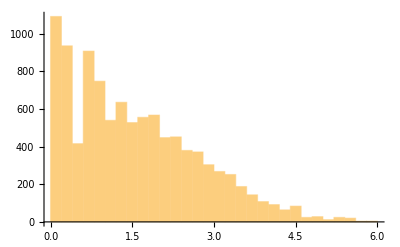

```mathematica
residuals=2 Abs[comparison[[;;,1]]-comparison[[;;,2]]]/Abs[comparison[[;;,1]]+comparison[[;;,2]]];
Mean[residuals]
Variance[residuals]
Total[residuals]
Total[residuals^2]
{Min[residuals],Max[residuals]}
Histogram[residuals]
```